# Experiments testing my Bayesian denoising algorithm

## Prior distribution

To make things concrete, I will assume the following distribution of peaks.  (I can substitute other priors, these are just ones that sounded reasonable to me based on a quick inspection of two regions in the ANIT data.)

The two bins in my data set were 0.0180 and 0.0360 ppm wide respectively and held an average of 2 and 6 peaks respectively.  The bins were located at (2.922,2.940) and (1.319,1.3550) ppm respectively.  I looked at only 3 spectra.  I did a targeted deconvolution of these bins for my spectra.  The sampling interval was 0.00043 ppm between samples.  So,  the bins were 41.9 and 83.7 samples wide respectively.  This means that an interval of 128 samples approximates a single bin width.

### Raw data

Mode amplitude:

```mathematica
originalPeakHeights={0.253986583252959,0.0553537869547886, 0.319990025528050, 0.0537642439994342 ,0.299216105545135 ,0.114271593179566 ,0.0132098897572650, 0.0647117135804350 ,0.00244445364511030, 0.0617927614203400 ,0.00858198526175317 ,0.0129712511578383 ,0.0470612345135570 ,0.00189137745148881 ,0.0567594344541371 ,0.00373301702195819 ,0.00374603410170547, 0.0116727709727065 ,0.0142319241486256 ,0.0795167347788190 ,0.0172800906039553, 0.0748124539248162 ,0.0177671490428016 ,0.0149493479646242};
```

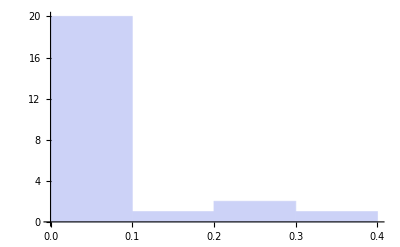

```mathematica
Histogram[originalPeakHeights]
```

```mathematica
Mean[originalPeakHeights]
```

0.0668215

```mathematica
originalPeakLorentzianness={0.455345279801903 ,0.888127571379308, 0.592024065234754 ,0.347454355895714 ,0.794075228953797, 0.547295491440938 ,0.379406914482378, 0.246193976011464 ,0.000254282672454725, 0.494931489923150, 0.0229765732912850 ,0.999999999999960, 6.50726812496324 10^-06 ,0.000996980550335289 ,0.584078380562258 ,3.36339230576405 10^-07, 1.94965902390985 10^-10 ,0.00478195133912706 ,0.999999760098370 ,0.973932969341911 ,0.999999259856875 ,0.999997989112487 ,6.15849524209445 10^-10, 6.52162245663082 10^-05}
```

{0.455345,0.888128,0.592024,0.347454,0.794075,0.547295,0.379407,0.246194,0.000254283,0.494931,0.0229766,1.,6.50727×10^-6,0.000996981,0.584078,3.36339×10^-7,1.94966×10^-10,0.00478195,1.,0.973933,0.999999,0.999998,6.1585×10^-10,0.0000652162}

Fraction that the peak is Lorentzian

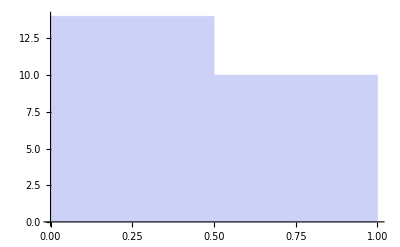

```mathematica
Histogram[originalPeakLorentzianness]
```

Width at half-height:

```mathematica
originalPeakGammas={0.00259129170842004 ,0.00279108048767069, 0.00244827759969623 ,0.00223070295065792 ,0.00193023630413313 ,0.00178176162034319 ,0.00339513234676295 ,0.00285998027914858 ,0.00167810359985705 ,0.00313331778139100 ,0.00486488532257895 ,0.00308274839379936 ,0.00265478331628142 ,0.00133151731831576 ,0.00267492429774681 ,0.00194762692549227 ,0.00196110663524006 ,0.00482346348435443 ,0.00306279796709518 ,0.00208576773078888 ,0.00245315117745186 ,0.00270948809557807 ,0.00287530106899310 ,0.00682218710561953};
```

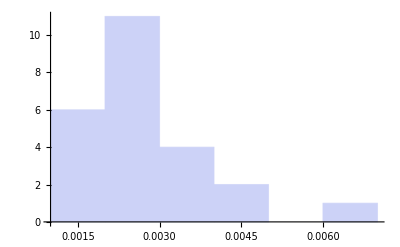

```mathematica
Histogram[originalPeakGammas]
```

Coincidentally, this shape resembles a gamma distribution.  I'll do a simple rough calculation of the parameters.  (I have no idea how good this estimator is, I just made it up on the spot)

```mathematica
Mean[originalPeakGammas]
```

0.00284123

```mathematica
Variance[originalPeakGammas]
```

1.43149×10^-6

Since the mean of a Gamma(k, θ) funciton is kθ and its variance is kθ^2, I can calculate k and theta. (θ is the scale parameter and k is the shape parameter)

```mathematica
Variance[originalPeakGammas]/Mean[originalPeakGammas]
```

0.000503828

```mathematica
Mean[originalPeakGammas]^2/Variance[originalPeakGammas]
```

5.63929

θ: 0.000503828  and k: 5.63929

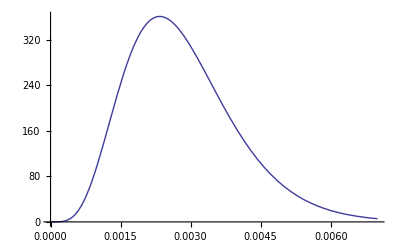

```mathematica
Plot[PDF[GammaDistribution[5.639291438052089,0.0005038283197638329]][x],{x,0,0.007}]
```

Here I scaled the plot to number of samples wide

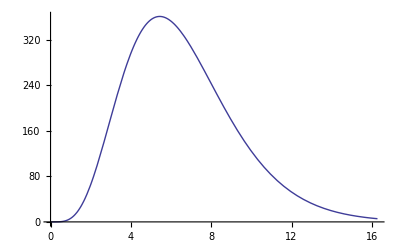

```mathematica
Plot[PDF[GammaDistribution[5.639291438052089,0.0005038283197638329]][x 0.00043],{x,0,0.007/0.00043}]
```

Locations:

```mathematica
originalPeakLocations={2.93299970572561, 2.92854525307565 ,2.93303774505893, 2.92863127666168 ,2.93236386760658, 2.92828684405938 ,1.32772682105547, 1.33438934814340 ,1.34108499999932, 1.34593379675646 ,1.35240916148288, 1.32696737800631 ,1.33334034017850, 1.34065499999996 ,1.34463069017209, 1.34891637724399 ,1.35355499999975, 1.35336829495003 ,1.34771863244973, 1.34326923167162 ,1.33953244033147, 1.33181006366878 ,1.32627606450301, 1.32144923190326};
```

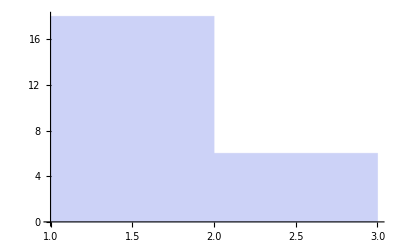

```mathematica
Histogram[originalPeakLocations]
```

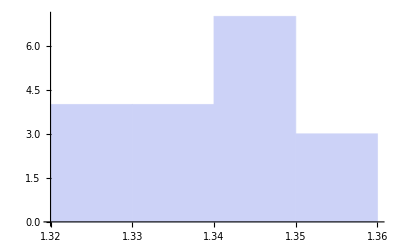

```mathematica
Histogram[Select[originalPeakLocations,#<2&]]
```

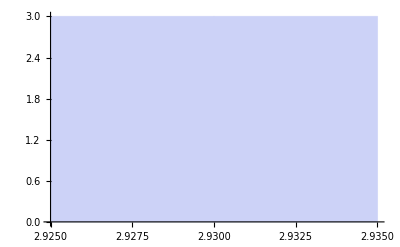

```mathematica
Histogram[Select[originalPeakLocations,#>2&]]
```

### The parameters I decided to use, having seen the raw data

number of peaks: Geometric[1/7] (mean=6)  (This gives a usually reasonable amount of peaks with the possiblity for severe congestion)  The geometric is the discrete version of the Exponential and the exponential is the maximum entropy distribution when the mean is known.  I chose this to be maximum entropy for a known mean peaks in a bin (which I derived loosely from looking at the data above)

ppm between samples: 0.00043 ppm

number of samples: 128

total sampled interval: 0.05504

Note that I choose the locations, heights, and gammas independently.  This is obviously not the case for real data.

peak locations = Uniform(0,0.05504)

peak heights = Exponential(mean=0.0668215)

peak half-height widths = Gamma[5.639291438052089`, 0.0005038283197638329`]

peak Lorentzianness = 1 (the real distribution I observed is Uniform[0,1] but I'd like to simplify the expressions a little now.  Later I'll make them more complex if the situation warants.)

number of divisions of the discrete amplitudes I will use: 256

range of the amplitudes: [0,1.70992].  (Gamma[k,θ] is the distribution of the sum of k independent exponential distributions with mean θ.  Since I have 12 peaks and their heights are exponentially distributed with the given mean, I can get 99.9% of their sums if I choose this range (and that is assuming the worst case that they all overlap at their peak - which is extremely unlikely)

```mathematica
N[Reduce[CDF[GammaDistribution[12,668215/10000000]][x]==999/1000,{x},Reals]]
```

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

GammaRegularized[12.,0.,14.9652 x]∈Reals&&(x==-0.260951||x==1.70992)

```mathematica
CDF[GammaDistribution[12,668215/10000000]][1.7099153356905117]
```

0.999

### Define the parameters

```mathematica
numPeakDist=GeometricDistribution[1/7];
```

```mathematica
ppmBetwSamps=0.00043;
```

```mathematica
numSamps=128;
```

```mathematica
sampledInterval=Interval[{0,0.05504}];
```

```mathematica
peakLocDist=UniformDistribution[sampledInterval[[1]]];
```

```mathematica
peakHeightDist=ExponentialDistribution[1/0.0668214984275779];
```

```mathematica
peakGammaDist=GammaDistribution[5.639291438052089,0.0005038283197638329];
```

```mathematica
numDiscreteAmplitudes=256;
```

```mathematica
amplitudeInterval=Interval[{0,1.7099153356905117}];
```

Amplitude bins gives the interval for which a number falls in any of the amplitude bins.  Since Intervals in Mathematica  are closed, one needs to find the first matching interval to do the discretization.  I also assume in this that there are no negative amplitudes.  The last bin is for amplitudes that were out of range.  I could probably increase the accuracy of my approximation if I used non-uniform bin-sizes throughout, concentrating on the smaller bins.

I can also increase the accuracy/decrease computation/decrease storage space if I make use of the fact that the amplitude probability distribution is band-diagonal

```mathematica
amplitudeBins=With[{n=numDiscreteAmplitudes-1,ai=amplitudeInterval},With[{d=(Max[ai]-Min[ai])/n},With[{borders=Range[Min[ai],Max[ai],d]},
With[{normalBins=Map[Interval[{borders[[#]],borders[[#+1]]}]&,Range[1,Length[borders]-1]]},
If[Length[borders]≥1,Join[normalBins,{Interval[{Last[borders],Infinity}]}],Interval[0,Infinity]]
]]]];
```

```mathematica
Length[amplitudeBins]
```

256

```mathematica
binNumberForA[amplitude_]:=With[{n=numDiscreteAmplitudes-1,ai=amplitudeInterval},With[{d=(Max[ai]-Min[ai])/n},
IntegerPart[(amplitude-Min[ai])/d]
]]
```

## Sampling from the Prior

Returns the value of the Lorentzian curve at the given point

```mathematica
lor[x_,amp_,γ_,loc_]:=amp γ^2/(4 (x-loc)^2+γ^2)
```

Returns the width of the given interval

```mathematica
width[i_Interval]:=Max[i]-Min[i]
```

Returns list of {x,y} pairs where the x is the sample position and the y is the sample amplitude

```mathematica
sampleFromPrior[]:=With[{numPeaks=RandomInteger[numPeakDist],samplePoints=Range[Min[sampledInterval],Max[sampledInterval],width[sampledInterval]/(numSamps-1)]},
With[{peakParams=Table[{RandomReal[peakHeightDist],RandomReal[peakGammaDist],RandomReal[peakLocDist]},{numPeaks}]},(*Print[peakParams];*)
Map[{#,Sum[lor[#,peakParams[[i,1]],peakParams[[i,2]],peakParams[[i,3]]],{i,1,numPeaks}]}&,samplePoints]
]]
```

#### Some actual samples from the prior

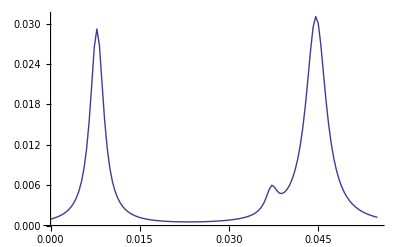
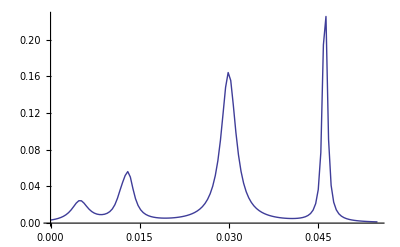
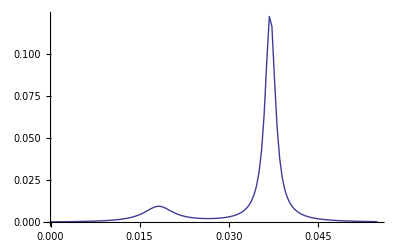
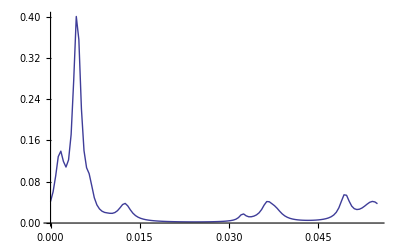
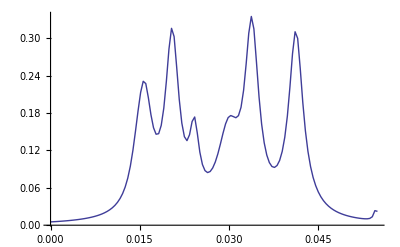
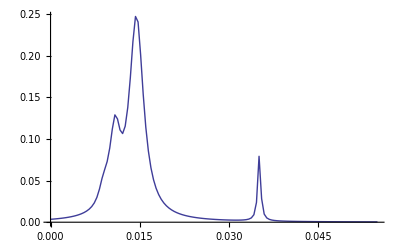
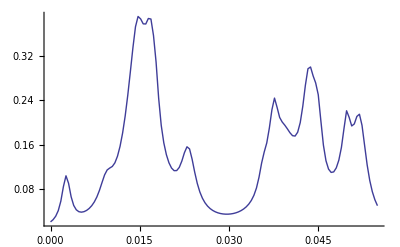
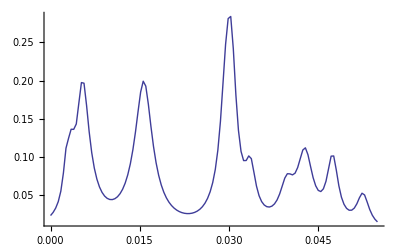

```mathematica
Table[ListLinePlot[sampleFromPrior[],PlotRange->All,AxesOrigin->{0,0}],{20}]
```

## Calculating the noise table

countA[i0,a0,a1] Gives the number of trials in which the sample at index i0 has value in the interval amplitudeBins[a0] and the sample at index i0+1 has a value in the interval amplitudeBins[a1]

```mathematica
(*This statement will initialize all the counts to 0.Table[countA[i0,a0,a1]=0,{i0,1,numSamps},{a0,1,numDiscreteAmplitudes},{a1,1,numDiscreteAmplitudes}];trialsA=0;*)
```

trialsA is the number of trials that have been made

```mathematica
Get["countAAndTrialsA.mx"];
```

```mathematica
DumpSave["countAAndTrialsA.mx",{countA,trialsA}]
```

Hold[Abort[],Abort[]]

```mathematica
Timing[With[{startTime=AbsoluteTime[]},
While[AbsoluteTime[]<startTime+10,
With[{f=Map[binNumberForA[#[[1]]]&,sampleFromPrior[]]},
trialsA=trialsA+1;
	MapIndexed[countA[#,f[[#]],f[[#+1]]]&
```

{12.2011,Null}